```mathematica
SetDirectory["D:\\Simha\\Computation & Codes\\Mathematica"]
```

D:\Simha\Computation & Codes\Mathematica

```mathematica
Get["BVPh2_0.m"]
```

Package BVPh.m was successfully loaded from D:\Simha\Computation & Codes\Mathematica\BVPh2_0.m !

Last updated by Yin-long Zhao, 00:22, Apr. 26, 2013.

The values of control parameters in BVPh:

Ntruncated  =  10

NtermMax    =  90

Nintegral   =  50

ErrReq      =  1.×10^-30

NgetErr     =  2

ComplexQ    =  0

PRN         =  1

ApproxQ     =  0

TypeL       =  TypeL

TypeBase    =  TypeBase

HYBRID      =  HYBRID

FLOAT       =  1

Naccu       =  100

About the system of ODEs:

It has 3 differential equation(s) subject to 6 boundary conditions.

(1) Governing equation(s):

1th ODE: -0.00625 F[z] g[z]^2-0.0125 F[z] h[z]^2+F''[z] = 0,

2th ODE: -0.00625 F[z]^2 g[z]-0.0125 g[z] h[z]^2+g''[z] = 0,

3th ODE: -0.00625 F[z]^2 h[z]-0.0015625 g[z]^2 h[z]+h''[z] = 0,

(2) Boundary conditions:

1th BC: -1+F[0] = 0,

2th BC: F'[0] = 0,

3th BC: -1+g[0] = 0,

4th BC: g'[0] = 0,

5th BC: -1+h[0] = 0,

6th BC: h'[0] = 0,

(3) Domain of the ODE:

1th ODE: 0 <= z <= 5

2th ODE: 0 <= z <= 5

3th ODE: 0 <= z <= 5

(4) Integral interval of the error:

1th ODE: 0 <= z <= 5

2th ODE: 0 <= z <= 5

3th ODE: 0 <= z <= 5

Convergence-control parameters in HAM:

(1) Initial guess(es):

u[1, 0] = 0

u[2, 0] = 0

u[3, 0] = 0

(2) Auxiliary linear operator(s):

L[1, u] = u''[z]

L[2, u] = u''[z]

L[3, u] = u''[z]

(3) Auxiliary function(s):

H[1, z] = 1

H[2, z] = 1

H[3, z] = 1

(4) Convergence-control parameter(s):

c0[1] = -12/5

c0[2] = -1/2

c0[3] = -9/5

Computing optimal values...

ApproxQ    = 0

TypeL      = TypeL

k = 1

k = 2

k = 3

k = 4

The minimum error at 4th order:

{0.,{c0[1.]→-2.4,c0[2.]→-0.5,c0[3.]→-1.8}}

Used CPU time = 0.659356 (seconds)

Computing higher order approximations...

ApproxQ    = 0

TypeL      = TypeL

k = 11

Used CPU time = 0.160433 (seconds)

k = 12

Err[12]= {2.77695×10^-22,4.63153×10^-22,1.12739×10^-25}

Used CPU time = 0.541963 (seconds)

k = 13

Used CPU time = 0.740755 (seconds)

k = 14

Err[14]= {1.94069×10^-21,6.84189×10^-22,5.61659×10^-25}

Used CPU time = 1.0692 (seconds)

k = 15

Used CPU time = 1.28554 (seconds)

k = 16

Err[16]= {9.56041×10^-21,7.41087×10^-22,1.2839×10^-24}

Used CPU time = 3.36184 (seconds)

k = 17

Used CPU time = 3.65617 (seconds)

k = 18

Err[18]= {4.12482×10^-20,7.46442×10^-22,2.63923×10^-24}

Used CPU time = 4.22922 (seconds)

k = 19

Used CPU time = 4.65579 (seconds)

k = 20

Err[20]= {1.67718×10^-19,7.31155×10^-22,6.06641×10^-24}

Used CPU time = 5.51164 (seconds)

Successful !

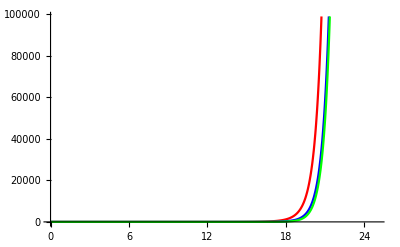

```mathematica
TypeEQ = 1;
NumEQ = 3;
f[1,z_,{F_,g_,h_},Lambda_]:=D[F,{z,2}]- B*F * g^2 -(G/4)*F*h^2;
f[2,z_,{F_,g_,h_},Lambda_]:=D[g,{z,2}]-A * g * F^2-(G/4)*g*h^2;
f[3,z_,{F_,g_,h_},Lambda_]:=D[h,{z,2}]-A * h * F^2-(B/4)*h*g^2;

(*              Define Boundary conditions          *)
NumBC = 6;
BC[1,z_,{F_,g_,h_}]:=(F-1)/.z->0;
BC[2,z_,{F_,g_,h_}]:=D[F,z]/.z->0;
BC[3,z_,{F_,g_,h_}]:=(g-1)/.z->0;
BC[4,z_,{F_,g_,h_}]:=D[g,z]/.z->0;
BC[5,z_,{F_,g_,h_}]:=(h-1)/.z->0;
BC[6,z_,{F_,g_,h_}]:=D[h,z]/.z->0;
zL[1]=0;
zR[1]=5;
zL[2]=0;
zR[2]=5;
zL[3]=0;
zR[3]=5;

(*                 Define initial guess             *)
U[1,0]=0;
U[2,0]=0;
U[3,0]=0;

(*          Define the auxiliary linear operator    *)
L[1,u_]:=D[u,{z,2}];
L[2,u_]:=D[u,{z,2}];
L[3,u_]:=D[u,{z,2}];

(*              Define physical parameters          *)
A=B= 0.00625;
G=0.05;
(*                  Print input data                *)
PrintInput[{F[z],g[z],h[z]}];

(*                  Get optimal c0                  *)
GetOptiVar[4,{},{c0[1],c0[2],c0[3]}];

(*          Gain 10th-order HAM approximation       *)
BVPh[11, 20]
Plot[{U[1,20],U[2,20],U[3,20]},{z,0,25},PlotStyle->{Red,Blue,Green}]
```

```mathematica
U[1,10]
```

U[1,10]

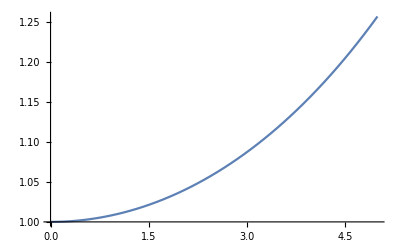

```mathematica
Plot[U[1,10],{z,0,5}]
```